# Dynamical Analysis of evolved ANN

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
Needs["PlotLegends`"]
<<"~thomasbuhrmann/Code/Mathematica/Dynamica/Dynamica.m";

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_11_11__17_27_02";(* inc12 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/ArmInp3H6/Pos2/13_12_04__11_29_53";(* test run with neuralinput in file *)


SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]]
numVars=Dimensions[varNames];
data = all[[2;;-2]];
numData=Length[data];

SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->14}];
```

Dynamica (Version 1.0.5 - 12/6/11), Copyright(c) 1993-2011 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

{NeuralExtInput0,NeuralExtInput1,NeuralExtInput10,NeuralExtInput11,NeuralExtInput12,NeuralExtInput2,NeuralExtInput3,NeuralExtInput4,NeuralExtInput5,NeuralExtInput6,NeuralExtInput7,NeuralExtInput8,NeuralExtInput9,NeuralInput0,NeuralInput1,NeuralInput10,NeuralInput11,NeuralInput12,NeuralInput2,NeuralInput3,NeuralInput4,NeuralInput5,NeuralInput6,NeuralInput7,NeuralInput8,NeuralInput9,NeuralOutput0,NeuralOutput1,NeuralOutput10,NeuralOutput11,NeuralOutput12,NeuralOutput2,NeuralOutput3,NeuralOutput4,NeuralOutput5,NeuralOutput6,NeuralOutput7,NeuralOutput8,NeuralOutput9,NeuralState0,NeuralState1,NeuralState10,NeuralState11,NeuralState12,NeuralState2,NeuralState3,NeuralState4,NeuralState5,NeuralState6,NeuralState7,NeuralState8,NeuralState9,accelerationElbow,accelerationShoulder,angleElbow,angleShoulder,coriolisElbow,coriolisShoulder,dampingElbow,dampingShoulder,elbX,elbY,gravityElbow,gravityShoulder,inertiaElbow,inertiaShoulder,interactionElbow,interactionShoulder,lineX1,lineX2,lineY1,lineY2,torqueElbow,torqueShoulder,velocityElbow,velocityShoulder,x,y}

## Config

```mathematica
numNeurons = Total[StringCount[varNames,"NeuralOutput"]];

dt =1/200;
T=12.0;
skip=0.0;
numTrials = Round[numData/(T/dt)];

SetTrial[trial_]:=Module[{},
t0=IntegerPart[1+(trial*T+skip)/dt];
tn= IntegerPart[t0+((T-skip)/dt)-1];
time=Range[tn-t0+1]*dt;
];

NtoI[name_]:=Position[varNames, name][[1,1]];
NtoD[name_]:=data[[t0;;tn,NtoI[name]]];

plotOptions = {PlotRange->All};

TimePlot[name_, options_, Scale_:1] := Module[{},
ListLinePlot[Transpose[{time,Scale*NtoD[name]}], Join[options,plotOptions]]
];

TimePlotT[name_, options_, tr_] := Module[{},SetTrial[tr];TimePlot[name,options,1]];

XYPlot[tr_,name1_,name2_, options_:{}] :=Module[{},
SetTrial[tr];
ListPlot[Transpose[{NtoD[name1],NtoD[name2]}], Join[options,plotOptions]]
];

MinExpand[x_,f_]:=If[x>=0,(1-f)*x,(1+f)*x];
MaxExpand[x_,f_]:=If[x>=0,(1+f)*x,(1-f)*x];
```

## CTRNN Definition

### Differential equations

General definition of the two-node network, and specialization via replacement rules.

```mathematica
σ[x_]=1/(1+ⅇ^-x);

maxp = 20;
maxy =15;

neuron= DynamicalSystem[
{(-y+w σ[y+θ]+J)/τ},
{{y,-maxy,maxy}},
{{w,-maxp,maxp},
{θ,-maxp,maxp},
{J,-maxy,maxy},
{τ,0.5,20}}];

couple =DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+J)/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2},
{{y1,-maxp,maxp},{y2,-maxp,maxp}},
{{w11,-maxp,maxp},{w12,-maxp,maxp},{w21,-maxp,maxp},{w22,-maxp,maxp},{θ1,-maxp,maxp},{θ2,-maxp,maxp},{τ1,0.5,20},{τ2,0.5,20},{J,-50,50}}];
```

### Specialization

```mathematica
neuron12 = neuron/.{w->-7.36998,θ->5.9649,τ->1.0,J->0};
neuron11 = neuron/.{w->-9.0286,θ->6.2327,τ->1.0,J->0};

neuron10=neuron/.{w->-0.765,θ->-6.2493,τ->1.0,J->0};
neuron9=neuron/.{w->-4.1,θ->-1.895,τ->1.0,J->0};
neuron8=neuron/.{w->-4.76,θ->-5.952,τ->1.0,J->0};
neuron7=neuron/.{w->7.8,θ->-1.2,τ->1.0,J->0};
neuron6=neuron/.{w->-6.9,θ->-9.31,τ->1.0,J->0};
neuron5=neuron/.{w->-7.67,θ->-8.972,τ->1.0,J->0};
neuron4=neuron/.{w->-1.82,θ->-1.95,τ->1.0,J->0};
neuron3=neuron/.{w->-8.83,θ->-3.96,τ->1.0,J->0};

outputs = {neuron11, neuron12};
hidden = {neuron3, neuron4, neuron5, neuron6, neuron7, neuron8, neuron9, neuron10};
neurons=Join[hidden,outputs];

inW=9.79266;

network = couple/.{w11->7.54563,w21->0,w12->-2.07816, w22->0.0,θ1->-4.0057,θ2->1.57389,τ1->1.0,τ2->1.0,J->0};
With[{ε=10^-7},networko=TransformDynamicalSystem[network,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]];
With[{ε=10^-7},output1o=TransformDynamicalSystem[output1,{{o,ε,1-ε}},{σ[y+θ]}]];
With[{ε=10^-7},output2o=TransformDynamicalSystem[output2,{{o,ε,1-ε}},{σ[y+θ]}]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

### Output neuron phase portraits

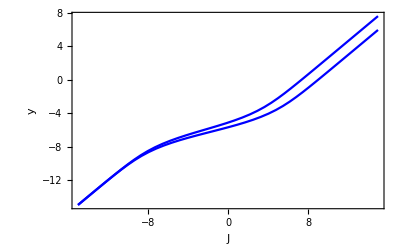

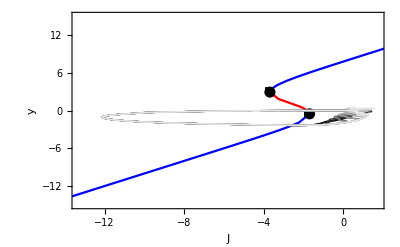

```mathematica
input=0;

Show[DisplayBifurcationDiagram[outputs[[1]],J],DisplayBifurcationDiagram[outputs[[2]],J]]

BifPhasePlot[i_]:=Module[{},
bif=DisplayBifurcationDiagram[neurons[[i-2]],J];
mi=Min[data[[All,NtoI["NeuralInput"<>ToString[i]]]]];
ma=Max[data[[All,NtoI["NeuralInput"<>ToString[i]]]]];
trajs=Show[Table[XYPlot[tr,"NeuralInput"<>ToString[i],"NeuralState"<>ToString[i],{Joined->True,PlotStyle->GrayLevel[tr/10]}],{tr,0,9}]];
Show[bif, trajs,PlotRange->{{MinExpand[mi,0.1],MaxExpand[ma,0.1]},Automatic}]
];

BifPhasePlot[7]
```

### Hidden neuron bifurcation diagram

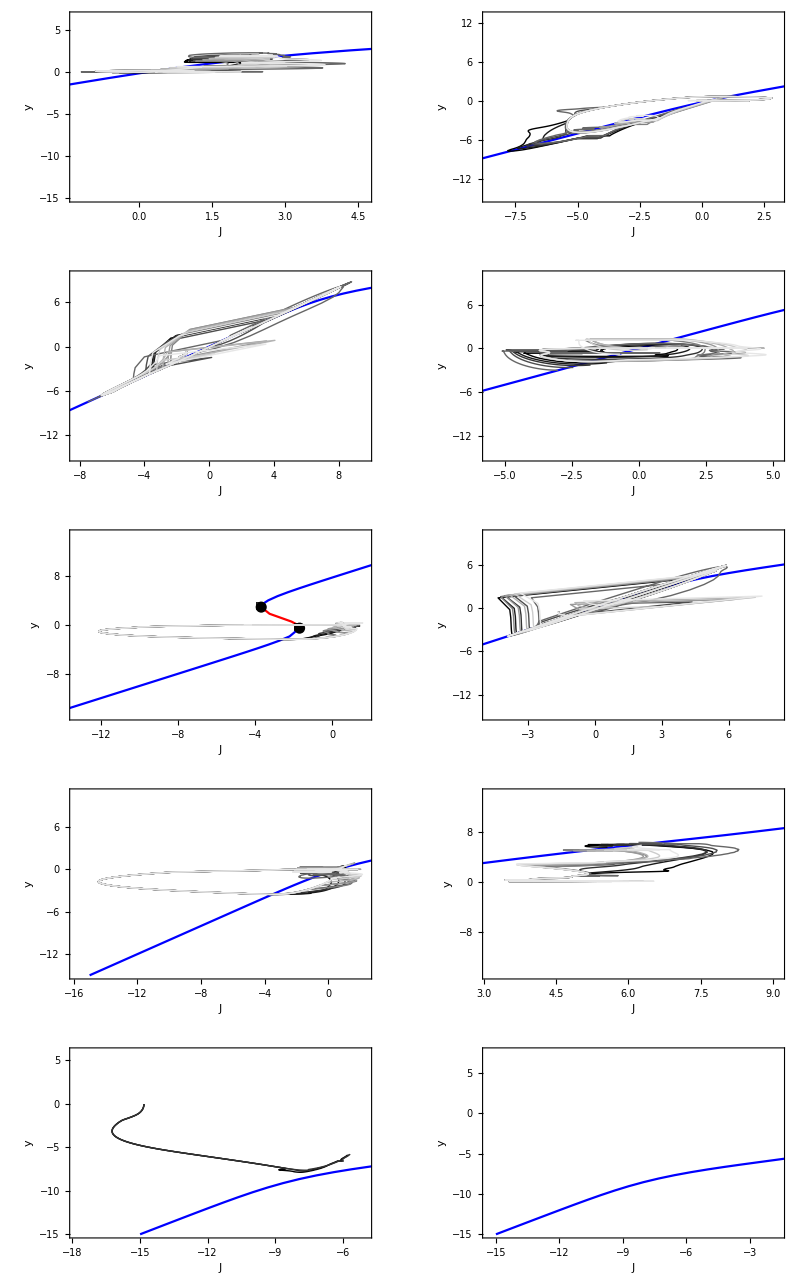

```mathematica
(*GraphicsGrid[Partition[Table[DisplayBifurcationDiagram[hidden[[i]],J],{i,1,8}],4],ImageSize->800]*)
GraphicsGrid[Partition[Table[BifPhasePlot[i],{i,3,12}],2],ImageSize->800]
(*bifPl=DisplayBifurcationDiagram[hidden,J,GridLinesStyle->Dashed,GridLines->{{0},{0}}];
$BifurcationDiagramBPs*)
```